Evolutionary Optimization With Irreversibility Constraint Govern by Poisson’s Equation
Author: Nha Tran
Department of Mathematics
Louisiana State University
Baton Rouge, LA, 70803
email: vtran32(at)lsu(dot)edu/ tvnha(dot)hcmus(at)gmail(dot)com

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Delete All Output;
```

```mathematica
Clear["Global`*"]
```

## The Problem

The prescribed displacement is given, d(t, x). Suppose the displacement solution is separable. We are looking for an ansatz displacement, u(t, x) = X(t) Y(x), which is an piecewise increasing function. Therefore, the slopes, a,b should be all positive. The solution branch at t = t0, where 0<= t0 <= T. They are given as follows

```mathematica
(* T= 1; k = 200;  tStar = 1-1/Sqrt[2]; N[tStar]; *)
d[k_, t_, x_]:= Piecewise[{{k/2*t*x*(1-x),t≤T/2},{k/2*(T-t)*x*(1-x),t>T/2}}];
u[a_, b_, t_, x_, t0_]:= Piecewise[{{1/2*a*t*x*(1-x),t≤t0},{1/2*(b*(t - t0)+ a*t0)*x*(1-x),t>t0}}];
```

Remark: It is noticed that T and k are given. Print out the two branches of the ansatz displacement to see if they work properly

```mathematica
Simplify[Refine[u[a,b, t, x, t0],t>t0]]; (*Remove the semicolon to see the results*)
Simplify[Refine[u[a, b,t, x, t0],t<t0]];
```

Plot the prescribed displacement

```mathematica
preDis = Plot3D[d[k,t, x]/.{T->1, k->200},{t,0,1}, {x,0,1}, AxesOrigin->{0,0},AxesLabel->{t,x, J}, PlotStyle->Directive[Gray,Specularity[White,40]]]
Export[NotebookDirectory[]<>"evol_figures/prescribed_displacement.pdf",preDis];
```

-Graphics3D-

## Case 1: t0 <= T/2

### The General Case: a, b are non zeros

#### The Objective function

```mathematica
JJ1 = Simplify[Integrate[Integrate[(Refine[u[a,b, t, x, t0],t<t0] - Refine[d[k, t, x],t<T/2])^2,{x,0,1}],{t, 0, t0}] + Integrate[Integrate[(Refine[u[a,b, t, x, t0],t>t0] - Refine[d[k, t, x],t<T/2])^2,{x,0,1}],{t, t0, T/2}] + Integrate[Integrate[(Refine[u[a,b,  t, x, t0],t>t0] - Refine[d[k, t, x],t>T/2])^2,{x,0,1}],{t, T/2, T}]];
```

```mathematica
J1 [k_,a_, b_, T_, t0_] := Evaluate[JJ1]
J1 [k,a, b, T, t0]
```

(k^2 T^3+4 b^2 (T-t0)^3+12 a b (T-t0)^2 t0+4 a^2 (3 T-2 t0) t0^2+b k (-3 T^3+6 T^2 t0-4 t0^3)+a k (-6 T^2 t0+4 t0^3))/1440

#### The Gradient

```mathematica
gradJ1 = Simplify[D[J1[k,a,b, T, t0],{{a,b,t0}}]]
```

{1/720 t0 (6 b (T-t0)^2+4 a (3 T-2 t0) t0+k (-3 T^2+2 t0^2)),(8 b (T-t0)^3+12 a (T-t0)^2 t0+k (-3 T^3+6 T^2 t0-4 t0^3))/1440,1/240 (a-b) (2 b (T-t0)^2+4 a (T-t0) t0-k (T^2-2 t0^2))}

#### The Critical Points

```mathematica
criticalPointsJ1=Solve[{gradJ1[[1]]==0,gradJ1[[2]]==0, gradJ1[[3]]==0}, {a,b, t0}]
```

{{a→(3 k)/8,b→(3 k)/8,t0→0},{a→k,b→-k,t0→T/2},{a→(3 k)/8,b→(3 k)/8,t0→-√(3/5) T},{a→(3 k)/8,b→(3 k)/8,t0→√(3/5) T}}

#### The Hessian

```mathematica
hessJ1 = Simplify[D[J1[k,a,b, T, t0],{{a, b, t0}},{{a, b, t0}}]];
```

#### Check if the critical points minimize the objective function. Given: T = 1, k = 200

Check the first critical point

```mathematica
C11= Simplify[hessJ1/.{k->200,a->3*200/8,b->3*200/8,  T->1,t0->0}];
PositiveDefiniteMatrixQ[C11];
```

Check the second critical point. Remark: This point violate the irreversibility condition (b>=0), so we exclude it anyway

```mathematica
C12= Simplify[hessJ1/.{k->200,a->200,b->-200,  T->1,t0->0.5}];
PositiveDefiniteMatrixQ[C12];
```

Check the third critical point. Remark: t0 should be positive. Exclude this point as well

```mathematica
C13= Simplify[hessJ1/.{k->200,a->3*200/8,b->3*200/8,  T->1,t0->-Sqrt[3/5]}];
PositiveDefiniteMatrixQ[C13];
```

Check the fourth critical point. Remark: Exclude this point since t0>T/2

```mathematica
C14= Simplify[hessJ1/.{k->200,a->3*200/8,b->3*200/8,  T->1,t0->Sqrt[3/5]}];
PositiveDefiniteMatrixQ[C14];
```

### Case 1a: a != 0, b = 0

```mathematica
Clear["T", "k", "a","b", "t0"]
```

#### The Objective function

```mathematica
J1aAnotheWay = Simplify[Integrate[Integrate[(Refine[u[a,0, t, x, t0],t<t0] - Refine[d[k, t, x],t<T/2])^2,{x,0,1}],{t, 0, t0}] + Integrate[Integrate[(Refine[u[a,0, t, x, t0],t>t0] - Refine[d[k, t, x],t<T/2])^2,{x,0,1}],{t, t0, T/2}] + Integrate[Integrate[(Refine[u[a,0,  t, x, t0],t>t0] - Refine[d[k, t, x],t>T/2])^2,{x,0,1}],{t, T/2, T}]];
```

```mathematica
J1a[k_, a_, T_, t0_] := Evaluate[J1[k,a,b,T, t0]/.{ b->0}]
J1a[k,a,T,t0]
```

(k^2 T^3+4 a^2 (3 T-2 t0) t0^2+a k (-6 T^2 t0+4 t0^3))/1440

```mathematica
J1aPlot = Plot3D[J1a[k,a,T, t0]/.{ k->200,T->1},{a,0,300}, {t0,0,0.5}, AxesOrigin->{0,0},AxesLabel->{a,t0}, PlotStyle->Directive[Gray,Specularity[White,40]]];
```

```mathematica
contourPlotJ1a = ContourPlot[J1a[k,a,T, t0]/.{ k->200,T->1},{a,0,300},{t0,0,0.5},ContourLabels->All, PlotLegends->Automatic, FrameLabel->{a, t0}];
Export[NotebookDirectory[]<>"evol_figures/cost_case1a_contour_plot.pdf",contourPlotJ1a];
```

#### The Gradient

```mathematica
gradJ1a = Simplify[D[J1a[k,a, T, t0],{{a,t0}}]]
```

{1/720 t0 (4 a (3 T-2 t0) t0+k (-3 T^2+2 t0^2)),1/240 a (4 a (T-t0) t0-k (T^2-2 t0^2))}

#### The Critical Points

```mathematica
criticalPointsJ1a=Solve[{gradJ1a[[1]]==0,gradJ1a[[2]]==0}, {a, t0}]
```

{{a→0,t0→0},{a→0,t0→-√(3/2) T},{a→0,t0→√(3/2) T},{a→k,t0→1/2 (2 T-√2 T)},{a→k,t0→1/2 (2 T+√2 T)}}

#### The Hessian

```mathematica
hessJ1a = Simplify[D[J1a[k,a, T, t0],{{a, t0}},{{a, t0}}]];
```

#### Check if the critical points minimize the objective function. Given: T = 1, k = 200

Check the first critical point

```mathematica
C1a1= Simplify[hessJ1a/.{k->200,a->0,  T->1,t0->0}]
PositiveDefiniteMatrixQ[C1a1]
```

{{0,-5/6},{-5/6,0}}

False

Check the second critical point

```mathematica
C1a2= Simplify[hessJ1a/.{k->200,a->0,  T->1,t0->-Sqrt[3/2]}];
PositiveDefiniteMatrixQ[C1a2];
```

Check the third critical point

```mathematica
C1a3= Simplify[hessJ1a/.{k->200,a->0,  T->1,t0->Sqrt[3/2]}];
PositiveDefiniteMatrixQ[C1a3];
```

Check the fourth critical point. The optimal point

```mathematica
C1a4= Simplify[hessJ1a/.{k->200,a->200,  T->1,t0->1/2 (2 -√2 )}]
PositiveDefiniteMatrixQ[C1a4]
```

{{1/360 (-1+√2),5/3 (-1+√2)},{5/3 (-1+√2),(1000 √2)/3}}

True

Check the fifth critical point

```mathematica
C1a5= Simplify[hessJ1a/.{k->200,a->200,  T->1,t0->1/2 (2 +√2 )}];
PositiveDefiniteMatrixQ[C1a5];
```

#### Check the relative extrema on the boundaries (i.e. a=0, t0 = 0, and t0 = T/2)

```mathematica
J1a1[k_, a_, T_] := Evaluate[J1a[k,a,T, t0]/.{ t0->0}]
J1a1[k,a,T];
N[J1a1[k,a,T]/.{k->200, T->1}];
```

```mathematica
J1a2[k_,a_,T_] := Evaluate[J1a[k,a,T, t0]/.{ t0->T/2}]
Simplify[J1a2[k,a, T]];
```

```mathematica
gradJ1a2 = Simplify[D[J1a2[k,a, T],{{a}}]];
```

```mathematica
criticalPointsJ1a2=Solve[{gradJ1a2[[1]]==0}, {a}]
```

{{a→(5 k)/8}}

```mathematica
Simplify[J1a2[k,a, T]/.{k->200, a->5*200/8, T->1}];
```

```mathematica
N[%]
```

6.07639

```mathematica
FindMinimum[J1a2[k,a,T]/.{k->200, T->1}, {{a, 0.5}}]
```

{6.07639,{a→125.}}

```mathematica
J1a3[k_, T_, t0_] := Evaluate[J1a[k,a,T, t0]/.{ a->0}]
J1a3[k,T, t0];
N[J1a3[k,T, t0]/.{k->200, T->1}];
```

Therefore, the optimal value at the case 1a is

```mathematica
Simplify[J1a[k,a,T,t0]/.{k->200,a->200,  T->1,t0->1/2 (2 -√2 )}]
```

-250/9 (-3+2 √2)

```mathematica
N[J1a[k,a,T,t0]/.{k->200,a->200,  T->1,t0->1/2 (2 -√2 )}]
```

4.76591

### Case 1b: a = 0, b != 0

```mathematica
Clear["T", "k", "a","b", "t0"]
```

#### The Objective function

```mathematica
J1bAnotherWay = Simplify[Integrate[Integrate[(Refine[u[0,b, t, x, t0],t<t0] - Refine[d[k, t, x],t<T/2])^2,{x,0,1}],{t, 0, t0}] + Integrate[Integrate[(Refine[u[0,b, t, x, t0],t>t0] - Refine[d[k, t, x],t<T/2])^2,{x,0,1}],{t, t0, T/2}] + Integrate[Integrate[(Refine[u[0,b,  t, x, t0],t>t0] - Refine[d[k, t, x],t>T/2])^2,{x,0,1}],{t, T/2, T}]];
```

```mathematica
J1b[k_, b_, T_, t0_] := Evaluate[J1[k,a,b,T, t0]/.{ a->0}]
J1b[k,b,T,t0]
```

(k^2 T^3+4 b^2 (T-t0)^3+b k (-3 T^3+6 T^2 t0-4 t0^3))/1440

```mathematica
J1bPlot = Plot3D[J1b[k,b,T, t0]/.{ k->200,T->1},{b,0,300}, {t0,0,0.5}, AxesOrigin->{0,0},AxesLabel->{b,t0}, PlotStyle->Directive[Gray,Specularity[White,40]]];
```

```mathematica
contourPlotJ1b = ContourPlot[J1b[k,b,T, t0]/.{ k->200,T->1},{b,0,300},{t0,0,0.5},ContourLabels->All, PlotLegends->Automatic, FrameLabel->{b, t0}];
Export[NotebookDirectory[]<>"evol_figures/cost_case1b_contour_plot.pdf",contourPlotJ1b];
```

```mathematica
J1b[k,b,T,t0]/.{k->200,T->1}
```

(40000+4 b^2 (1-t0)^3+200 b (-3+6 t0-4 t0^3))/1440

#### The Gradient

```mathematica
gradJ1b = Simplify[D[J1b[k,b, T, t0],{{b,t0}}]]
```

{(8 b (T-t0)^3+k (-3 T^3+6 T^2 t0-4 t0^3))/1440,1/240 b (-2 b (T-t0)^2+k (T^2-2 t0^2))}

#### The Critical Points

```mathematica
criticalPointsJ1b=Solve[{gradJ1b[[1]]==0,gradJ1b[[2]]==0}, {b, t0}];
```

#### The Hessian

```mathematica
hessJ1b = Simplify[D[J1b[k,b, T, t0],{{b, t0}},{{b, t0}}]];
```

#### Check if the critical points minimize the objective function. Given: T = 1, k = 200

Check the critical point where t0 is a real number

```mathematica
C1b1= Simplify[hessJ1b/.{k->200,b->-1/2^(2/3)-1/2^(1/3), T->1,t0->0}];
PositiveDefiniteMatrixQ[C1b1];
```

#### Check the relative extrema on the boundaries (i.e. b=0, t0 = 0, and t0 = T/2)

It is clear from the previous plot that we can find the minimum of this case on the boundary at t0 = 0.

```mathematica
J1b1[k_, b_, T_] := Evaluate[J1b[k,b,T, t0]/.{ t0->0}]
Simplify[J1b1[k,b,T]];
```

```mathematica
gradJ1b1 = Simplify[D[J1b1[k,b, T],{{b}}]];
```

```mathematica
criticalPointsJ1b1=Solve[{gradJ1b1[[1]]==0}, {b}]
```

{{b→(3 k)/8}}

```mathematica
Simplify[J1b1[k,b, T]/.{k->200, b->3*200/8, T->1}];
N[%]
```

12.1528

```mathematica
J1b2[k_,b_,T_] := Evaluate[J1b[k,b,T, t0]/.{ t0->T/2}]
Simplify[J1b2[k,b, T]];
```

```mathematica
gradJ1b2 = Simplify[D[J1b2[k,b, T],{{b}}]];
```

```mathematica
criticalPointsJ1b2=Solve[{gradJ1b2[[1]]==0}, {b}]
```

{{b→k/2}}

```mathematica
Simplify[J1b2[k,b, T]/.{k->200, b->200/2, T->1}]
```

875/36

```mathematica
N[%];
```

```mathematica
FindMinimum[J1b2[k,b,T]/.{k->200, T->1}, {{b, 0.5}}]
```

{24.3056,{b→100.}}

```mathematica
J1b3[k_, T_, t0_] := Evaluate[J1b[k,b,T, t0]/.{ b->0}]
J1b3[k,T, t0];
N[J1b3[k,T, t0]/.{k->200, T->1}];
```

Therefore, the optimal value at the case 1b is

```mathematica
N[J1b[k,b,T,t0]/.{k->200,b->3*200/8,  T->1,t0->0}]
```

12.1528

### Case 1c: t0=0. Remark: this is the simplest case of the displacement field which is a linear increasing function.

```mathematica
Clear["T", "k", "a","b", "t0"]
```

#### The Objective function

```mathematica
J1cAnotherWay = Simplify[Integrate[Integrate[(Refine[u[0,b, t, x, 0],t>0] - Refine[d[k, t, x],t<T/2])^2,{x,0,1}],{t, 0, T/2}] + Integrate[Integrate[(Refine[u[0,b,  t, x, 0],t>0] - Refine[d[k, t, x],t>T/2])^2,{x,0,1}],{t, T/2, T}]];
```

```mathematica
J1c[k_, b_, T_] := Evaluate[J1[k,a,b,T, t0]/.{  t0->0}]
Simplify[J1c[k,b,T]]
```

((4 b^2-3 b k+k^2) T^3)/1440

#### The Gradient

```mathematica
gradJ1c = Simplify[D[J1c[k, b,T],{{b}}]]
```

{((8 b-3 k) T^3)/1440}

#### The Critical Points

```mathematica
criticalPointsJ1c=Solve[{gradJ1c[[1]]==0}, { b}]
```

{{b→(3 k)/8}}

#### The Hessian

```mathematica
hessJ1c = Simplify[D[J1c[k, b,T],{{ b}},{{ b}}]]
```

{{T^3/180}}

#### Check if the critical points minimize the objective function. Given: T = 1, k = 200

Check the first critical point

```mathematica
C1c= Simplify[hessJ1c/.{k->200,b->3*200/8,  T->1}]
PositiveDefiniteMatrixQ[C1c]
```

{{1/180}}

True

#### Some plots for this case

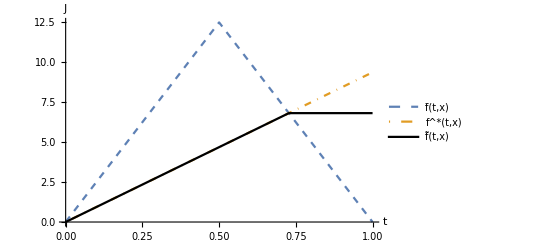

```mathematica
simplestDis=Plot[{d[k,t, x]/.{ T->1,k->200, x->0.5}, u[a, b,t, x, t0]/.{ t0->0,k->200, b->3*200/8,x->0.5}, u[a, b,t, x, t0]/.{ a->3*200/8,k->200, b->0,x->0.5, t0->8/11}}, {t, 0, 1}, PlotRange->All,AxesOrigin->{0,0}, PlotLegends->{ToExpression["\\bar{f}(t, x)",TeXForm,HoldForm],ToExpression["f^\\ast(t, x)",TeXForm,HoldForm], ToExpression["\\tilde{f} (t, x)",TeXForm,HoldForm]}, AxesLabel->{t,J}, PlotStyle->{Dashed, DotDashed,Black}]
Export["evol_figures/simplest_ansatz_evol.pdf",simplestDis];
```

Remark: The intersection point is at t0 = 8T/11

#### Evaluate some function values

The minimum value of the objective function is

```mathematica
J1c[k,b,T]/.{b->3*200/8}
J1c[k,b,T]/.{k->200,b->3*200/8,  T->1}
```

(22500 T^3-225 k T^3+k^2 T^3)/1440

875/72

```mathematica
N[%];
```

```mathematica
Simplify[J1 [k,a, b, T, t0]/.{a->3*200/8,b->0,t0->8 T/11} (*t0 = 8T/11*)]
J1 [k,a, b, T, t0]/.{k->200,a->3*200/8,b->0,t0->8/11,T->1} (*t0 = 8T/11*)
```

((24480000-282000 k+1331 k^2) T^3)/1916640

133250/11979

```mathematica
N[%]
```

11.1236

### Case 1d: t0=T/2

```mathematica
Clear["T", "k", "a","b", "t0"]
```

#### The Objective function

```mathematica
J1dAnotheWay = Simplify[Integrate[Integrate[(Refine[u[a,b, t, x, T/2],t<T/2] - Refine[d[k, t, x],t<T/2])^2,{x,0,1}],{t, 0, T/2}] + Integrate[Integrate[(Refine[u[a,b,  t, x, T/2],t>T/2] - Refine[d[k, t, x],t>T/2])^2,{x,0,1}],{t, T/2, T}]];
```

```mathematica
J1d[k_, a_,b_, T_] := Evaluate[J1[k,a,b,T, t0]/.{ t0->T/2}]
Simplify[J1d[k,a,b,T]]
```

((4 a^2+3 a b+b^2-5 a k-b k+2 k^2) T^3)/2880

```mathematica
J1dPlot = Plot3D[J1d[k,a,b,T]/.{ k->200,T->1},{a,0,300}, {b,0,300}, AxesOrigin->{0,0},AxesLabel->{a,b}, PlotStyle->Directive[Gray,Specularity[White,40]]];
```

```mathematica
contourPlotJ1d = ContourPlot[J1d[k,a, b,T]/.{ k->200,T->1},{a,0,300},{b,0,300},ContourLabels->All, PlotLegends->Automatic, FrameLabel->{a, b}];
Export[NotebookDirectory[]<>"evol_figures/cost_case1d_contour_plot.pdf",contourPlotJ1d];
```

#### The Gradient

```mathematica
gradJ1d = Simplify[D[J1d[k,a,b, T],{{a,b}}]]
```

{((8 a+3 b-5 k) T^3)/2880,((3 a+2 b-k) T^3)/2880}

#### The Critical Points

```mathematica
criticalPointsJ1d=Solve[{gradJ1d[[1]]==0,gradJ1d[[2]]==0}, {a, b}]
```

{{a→k,b→-k}}

#### The Hessian

```mathematica
hessJ1d = Simplify[D[J1d[k,a,b, T],{{a, b}},{{a, b}}]]
```

{{T^3/360,T^3/960},{T^3/960,T^3/1440}}

#### Check if the critical points minimize the objective function. Given: T = 1, k = 200

Check the critical point

```mathematica
C1d= Simplify[hessJ1d/.{k->200,a->200,b->-200, T->1}];
PositiveDefiniteMatrixQ[C1d];
```

The minimum value in this case

```mathematica
Simplify[J1d[k,a,b,T]/.{k->200,a->200,b->-200, T->1}];
```

```mathematica
Simplify[J1d[k,a,b,T]/.{k->200, a->0, b->0,T->1}]
```

250/9

```mathematica
N[%]
```

27.7778

#### Check the relative extrema on the boundaries (i.e. a=0 and b = 0)

It is clear from the previous plot that we can find the minimum of this case on the boundary at b= 0.

```mathematica
J1d1[k_,a_, T_] := Evaluate[J1d[k,a,b,T]/.{ b->0}]
Simplify[J1d1[k,a,T]]
```

((4 a^2-5 a k+2 k^2) T^3)/2880

```mathematica
gradJ1d1 = Simplify[D[J1d1[k,a, T],{{a}}]]
```

{((8 a-5 k) T^3)/2880}

```mathematica
criticalPointsJ1d1=Solve[{gradJ1d1[[1]]==0}, {a}]
```

{{a→(5 k)/8}}

```mathematica
Simplify[J1d1[k,a, T]/.{k->200, a->5*200/8, T->1}]
N[%]
```

875/144

6.07639

```mathematica
J1d2[k_,b_,T_] := Evaluate[J1d[k,a,b,T]/.{ a->0}]
Simplify[J1d2[k,b, T]];
```

```mathematica
gradJ1d2 = Simplify[D[J1d2[k,b, T],{{b}}]]
```

{((2 b-k) T^3)/2880}

```mathematica
criticalPointsJ1d2=Solve[{gradJ1d2[[1]]==0}, {b}]
```

{{b→k/2}}

```mathematica
Simplify[J1d2[k,b, T]/.{k->200, b->200/2, T->1}]
```

875/36

```mathematica
N[%]
```

24.3056

```mathematica
FindMinimum[J1d2[k,b,T]/.{k->200, T->1}, {{b, 0.5}}]
```

{24.3056,{b→100.}}

Therefore, the optimal value at the case 1d is

```mathematica
Simplify[J1d[k,a,b,T]/.{k->200,a->5*200/8,b->0,  T->1, t0->0.5}]
N[%]
```

875/144

6.07639

## Case 2: t0 > T/2

### The General Case: a, b are non zeros

#### The Objective function

```mathematica
JJ2= Simplify[Integrate[Integrate[(Refine[u[a,b, t, x, t0],t<t0] - Refine[d[k, t, x],t<T/2])^2,{x,0,1}],{t, 0, T/2}] + Integrate[Integrate[(Refine[u[a,b, t, x, t0],t<t0] - Refine[d[k, t, x],t>T/2])^2,{x,0,1}],{t, T/2, t0}] + Integrate[Integrate[(Refine[u[a,b,  t, x, t0],t>t0] - Refine[d[k, t, x],t>T/2])^2,{x,0,1}],{t, t0, T}]];
```

```mathematica
J2 [k_,a_, b_, T_, t0_] := Evaluate[JJ2]
Simplify[J2 [k,a, b, T, t0]]
```

((a-k)^2 T^3+(8 ((k (T-t0)-a t0)^3+(b (T-t0)+a t0)^3))/(b+k)+(8 (1/8 (-a+k)^3 T^3+(-k T+(a+k) t0)^3))/(a+k))/2880

#### The Gradient

```mathematica
gradJ2 = Simplify[D[J2[k,a,b, T, t0],{{a,b,t0}}]];
```

#### The Critical Points

```mathematica
criticalPointsJ2=Solve[{gradJ2[[1]]==0,gradJ2[[2]]==0, gradJ2[[3]]==0}, {a,b, t0}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a→(3 k)/8,t0→T},{a→-3 k,b→-k,t0→-T/2},{a→(3 k)/8,b→(3 k)/8,t0→(2 T)/11},{a→k,b→-k,t0→T/2}}

#### The Hessian

```mathematica
hessJ2 = Simplify[D[J2[k,a,b, T, t0],{{a, b, t0}},{{a, b, t0}}]];
```

#### Check if the critical points minimize the objective function. Given: T = 1, k = 200

Check the first critical point

```mathematica
C21= Simplify[hessJ2/.{k->200,a->3*200/8,b->0,  T->1,t0->1}]
PositiveDefiniteMatrixQ[C21]
```

{{1/180,0,0},{0,0,0},{0,0,-375/4}}

False

Check the second critical point. Remark: Violate the irreversibility condition. Exclude this point

```mathematica
C22= Simplify[hessJ2/.{k->200,a->-3*200,b->-200,  T->1,t0->-1/2}];
PositiveDefiniteMatrixQ[C22];
```

Check the third critical point

```mathematica
C23= Simplify[hessJ2/.{k->200,a->3*200/8,b->3*200/8,  T->1,t0->2/11}]
PositiveDefiniteMatrixQ[C23]
```

{{29/59895,27/26620,-45/88},{27/26620,81/26620,45/88},{-45/88,45/88,0}}

False

Check the fourth critical point. Remark: Violate the irreversibility condition. Exclude this point as well

```mathematica
C24= Simplify[hessJ2/.{k->200,a->200,b->-200,  T->1,t0->1/2}];
PositiveDefiniteMatrixQ[C24];
```

### Case 2a: a != 0, b = 0

```mathematica
Clear["T", "k", "a","b", "t0"]
```

#### The Objective function

```mathematica
J2aAnotheWay= Simplify[Integrate[Integrate[(Refine[u[a,0, t, x, t0],t<t0] - Refine[d[k, t, x],t<T/2])^2,{x,0,1}],{t, 0, T/2}] + Integrate[Integrate[(Refine[u[a,0, t, x, t0],t<t0] - Refine[d[k, t, x],t>T/2])^2,{x,0,1}],{t, T/2, t0}] + Integrate[Integrate[(Refine[u[a,0,  t, x, t0],t>t0] - Refine[d[k, t, x],t>T/2])^2,{x,0,1}],{t, t0, T}]];
```

```mathematica
J2a[k_, a_, T_, t0_] := Evaluate[J2[k,a,b,T, t0]/.{ b->0}]
Simplify[J2a[k,a,T,t0]]
```

(k^2 T^3+4 a^2 (3 T-2 t0) t0^2+a k (T^3-12 T^2 t0+12 T t0^2-4 t0^3))/1440

```mathematica
J2aPlot = Plot3D[J2a[k,a,T, t0]/.{ k->200,T->1},{a,0,300}, {t0,0.5,1}, AxesOrigin->{0,0},AxesLabel->{a,t0}, PlotStyle->Directive[Gray,Specularity[White,40]]];
```

```mathematica
contourPlotJ2a = ContourPlot[J2a[k,a, T, t0]/.{ k->200,T->1},{a,0,300},{t0,0.5,1},ContourLabels->All, PlotLegends->Automatic, FrameLabel->{a, t0}];
Export[NotebookDirectory[]<>"evol_figures/cost_case2a_contour_plot.pdf",contourPlotJ2a];
```

#### The Gradient

```mathematica
gradJ2a = Simplify[D[J2a[k,a, T, t0],{{a,t0}}]]
```

{(8 a (3 T-2 t0) t0^2+k (T^3-12 T^2 t0+12 T t0^2-4 t0^3))/1440,1/120 a (T-t0) (2 a t0+k (-T+t0))}

#### The Critical Points

```mathematica
criticalPointsJ2a=Solve[{gradJ2a[[1]]==0,gradJ2a[[2]]==0}, {a, t0}];
```

#### The Hessian

```mathematica
hessJ2a = Simplify[D[J2a[k,a, T, t0],{{a, t0}},{{a, t0}}]]
```

{{1/180 (3 T-2 t0) t0^2,-1/120 (T-t0) (k (T-t0)-4 a t0)},{-1/120 (T-t0) (k (T-t0)-4 a t0),1/60 a (a (T-2 t0)+k (T-t0))}}

#### Check if the critical points minimize the objective function. Given: T = 1, k = 200

Check the first critical point with real values

```mathematica
C2a1= Simplify[hessJ2a/.{k->200,a->3*200/8,  T->1,t0->1}]
PositiveDefiniteMatrixQ[C2a1]
```

{{1/180,0},{0,-375/4}}

False

Check the second critical point with real values

```mathematica
C2a2= Simplify[hessJ2a/.{k->200,a->0,  T->1,t0->1/2 (2 -6^(1/3) )}]
PositiveDefiniteMatrixQ[C2a2]
```

{{1/720 (10-3 6^(2/3)),-5/(2 6^(1/3))},{-5/(2 6^(1/3)),0}}

False

#### Check the relative extrema on the boundaries (i.e. t0=0.5 and t0 = 1)

```mathematica
FindMinimum[J2a[k,a,T, t0]/.{k->200, T->1, t0->0.5}, {{a, 0.5}}]
```

{6.07639,{a→125.}}

```mathematica
FindMinimum[J2a[k,a,T, t0]/.{k->200, T->1, t0->1}, {{a, 0.5}}]
```

{12.1528,{a→75.}}

### Case 2b: a = 0, b != 0

```mathematica
Clear["T", "k", "a","b", "t0"]
```

#### The Objective function

```mathematica
J2AnotherWay = Simplify[Integrate[Integrate[(Refine[u[0,b, t, x, t0],t<t0] - Refine[d[k, t, x],t<T/2])^2,{x,0,1}],{t, 0, T/2}] + Integrate[Integrate[(Refine[u[0,b, t, x, t0],t<t0] - Refine[d[k, t, x],t>T/2])^2,{x,0,1}],{t, T/2, t0}] + Integrate[Integrate[(Refine[u[0,b,  t, x, t0],t>t0] - Refine[d[k, t, x],t>T/2])^2,{x,0,1}],{t, t0, T}]];
```

```mathematica
J2b[k_, b_, T_, t0_] := Evaluate[J2[k,a,b,T, t0]/.{ a->0}]
Simplify[J2b[k,b,T,t0]]
```

(k^2 T^3+4 b^2 (T-t0)^3-4 b k (T-t0)^3)/1440

```mathematica
J2b[k,b,T,t0]/.{k->200,T->1}
```

(40000+(8 (8000000 (1-t0)^3+b^3 (1-t0)^3))/(200+b)+1/25 (1000000+(-200+200 t0)^3))/2880

```mathematica
J2bPlot = Plot3D[J2b[k,b,T, t0]/.{ k->200,T->1},{b,0,300}, {t0,0.5,1}, AxesOrigin->{0,0},AxesLabel->{b,t0}, PlotStyle->Directive[Gray,Specularity[White,40]]];
```

```mathematica
contourPlotJ2b = ContourPlot[J2b[k,b, T, t0]/.{ k->200,T->1},{b,0,300},{t0,0.5,1},ContourLabels->All, PlotLegends->Automatic, FrameLabel->{b, t0}];
Export[NotebookDirectory[]<>"evol_figures/cost_case2b_contour_plot.pdf",contourPlotJ2b];
```

#### The Gradient

```mathematica
gradJ2b = Simplify[D[J2b[k,b, T, t0],{{b,t0}}]]
```

{1/360 (2 b-k) (T-t0)^3,-1/120 b (b-k) (T-t0)^2}

#### The Critical Points

```mathematica
criticalPointsJ2b=Solve[{gradJ2b[[1]]==0,gradJ2b[[2]]==0}, {b, t0}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{t0→T}}

#### The Hessian

```mathematica
hessJ2b = Simplify[D[J2b[k,b, T, t0],{{b, t0}},{{b, t0}}]]
```

{{1/180 (T-t0)^3,-1/120 (2 b-k) (T-t0)^2},{-1/120 (2 b-k) (T-t0)^2,1/60 b (b-k) (T-t0)}}

#### Check if the critical points minimize the objective function. Given: T = 1, k = 200

Check the critical point where t0 is a real number

```mathematica
C2b= Simplify[hessJ2b/.{k->200, T->1,t0->1}]
PositiveDefiniteMatrixQ[C2b]
```

{{0,0},{0,0}}

False

Evaluate the function value

```mathematica
Simplify[J2b[k,b,T,t0]/.{k->200, T->1,t0->1}]
```

250/9

```mathematica
N[%]
```

27.7778

#### Check the relative extrema on the boundaries (i.e. t0 = 0.5, t0 =1, and a=0)

```mathematica
FindMinimum[J2b[k,b,T, t0]/.{k->200, T->1, t0->0.5}, {{b, 0.5}}]
```

{24.3056,{b→100.}}

```mathematica
FindMinimum[J2b[k,b,T, t0]/.{k->200, T->1, t0->1}, {{b, 0.5}}]
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{27.7778,{b→0.5}}

```mathematica
FindMinimum[J2b[k,b,T, t0]/.{k->200, T->1, b->0}, {{t0, 0.5}}]
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{27.7778,{t0→0.5}}

### Case 2c: t0=T/2 (Exactly the same as the case 1d)

```mathematica
Clear["T", "k", "a","b", "t0"]
```

#### The Objective function

```mathematica
J2cAnotherWay =
Simplify[Integrate[Integrate[(Refine[u[a,b, t, x, T/2],t<T/2] - Refine[d[k, t, x],t<T/2])^2,{x,0,1}],{t, 0, T/2}] + Integrate[Integrate[(Refine[u[a,b,  t, x, T/2],t>T/2] - Refine[d[k, t, x],t>T/2])^2,{x,0,1}],{t, T/2, T}]];
```

```mathematica
J2c[k_,a_, b_, T_] := Evaluate[J2[k,a,b,T, t0]/.{  t0->T/2}]
Simplify[J2c[k,a,b,T]]
```

((4 a^2+3 a b+b^2-5 a k-b k+2 k^2) T^3)/2880

#### The Gradient

```mathematica
gradJ2c = Simplify[D[J2c[k,a, b,T],{{a,b}}]]
```

{((8 a+3 b-5 k) T^3)/2880,((3 a+2 b-k) T^3)/2880}

#### The Critical Points

```mathematica
criticalPointsJ2c=Solve[{gradJ2c[[1]]==0}, { b}]
```

{{b→1/3 (-8 a+5 k)}}

#### The Hessian

```mathematica
hessJ2c = Simplify[D[J2c[k, a,b,T],{{a, b}},{{a, b}}]]
```

{{T^3/360,T^3/960},{T^3/960,T^3/1440}}

#### Check if the critical points minimize the objective function. Given: T = 1, k = 200

Check the critical point

```mathematica
C2c= Simplify[hessJ1d/.{k->200,a->200,b->-200, T->1}]
PositiveDefiniteMatrixQ[C2c]
```

{{1/360,1/960},{1/960,1/1440}}

True

The minimum value in this case

```mathematica
Simplify[J2c[k,a,b,T]/.{k->200,a->200,b->-200, T->1}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

### Case 2d: t0=T (Exactly the same as the case 1c)

```mathematica
Clear["T", "k", "a","b", "t0"]
```

#### The Objective function

```mathematica
J2dAnotherWay =
Simplify[Integrate[Integrate[(Refine[u[a,b, t, x, T],t<T] - Refine[d[k, t, x],t<T/2])^2,{x,0,1}],{t, 0, T/2}] + Integrate[Integrate[(Refine[u[a,b,  t, x, T],t<T] - Refine[d[k, t, x],t>T/2])^2,{x,0,1}],{t, T/2, T}]];
```

```mathematica
J2d[k_,a_,T_] := Evaluate[J2[k,a,b,T, t0]/.{  t0->T}]
Simplify[J2d[k,a,T]]
```

((4 a^2-3 a k+k^2) T^3)/1440

#### The Gradient

```mathematica
gradJ2d = Simplify[D[J2d[k,a,T],{{a}}]]
```

{((8 a-3 k) T^3)/1440}

#### The Critical Points

```mathematica
criticalPointsJ2d=Solve[{gradJ2d[[1]]==0}, { a}]
```

{{a→(3 k)/8}}

#### The Hessian

```mathematica
hessJ2d = Simplify[D[J2d[k, a,T],{{a}},{{a}}]]
```

{{T^3/180}}

#### Check if the critical points minimize the objective function. Given: T = 1, k = 200

Check the first critical point

```mathematica
C2d= Simplify[hessJ2d/.{k->200,a->3*200/8,  T->1}]
PositiveDefiniteMatrixQ[C2d]
```

{{1/180}}

True

The minimum value of the objective function is

```mathematica
J2d[k,a,T]/.{k->200,a->3*200/8,  T->1}
```

875/72

```mathematica
N[%]
```

12.1528

## Plot Some Results

```mathematica
Clear["T", "k", "a","b", "t0"]
```

```mathematica
pts={{200,N[1/2 (2 -√2 )]}};
```

```mathematica
J1aPlot = Plot3D[J1a[k,a,T, t0]/.{ k->200,T->1},{a,0,300}, {t0,0,0.5}, AxesOrigin->{0,0},AxesLabel->{a,ToExpression["t_0",TeXForm,HoldForm]}, PlotStyle->Directive[Gray,Specularity[White,40]]];
```

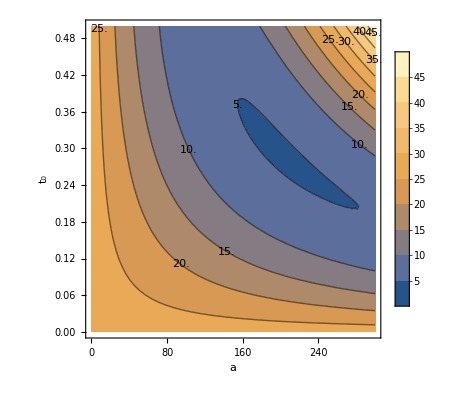

```mathematica
contourPlotCase1a = ContourPlot[J1a[k,a,T, t0]/.{ k->200,T->1},{a,0,300},{t0,0,0.5},ContourLabels->All, PlotLegends->Automatic, FrameLabel->{a, ToExpression["t_0",TeXForm,HoldForm]}]
Export[NotebookDirectory[]<>"evol_figures/cost_case1a_contour_plot.pdf",contourPlotCase1a];
```

Find a numeric result. Remark: This is also the result we found in the Case 1a

```mathematica
FindMinimum[J1a[200,200,1, t0], {{t0, 0.5}}]
```

{4.76591,{t0→0.292893}}

```mathematica
Simplify[J1a[200,200,1, 0.292893218813333]]
```

4.76591

```mathematica
contourPlotCase2a = ContourPlot[J2a[k,a,T, t0]/.{ k->200,T->1},{a,0,300},{t0,0.5,1},ContourLabels->All, PlotLegends->Automatic, FrameLabel->{a,ToExpression["t_0",TeXForm,HoldForm]},Contours->Function[{min,max},Range[min,max,5]]];
Export[NotebookDirectory[]<>"evol_figures/cost_case2a_contour_plot.pdf",contourPlotCase2a];
```

```mathematica
fig1 = Plot[J1a[k,a,T, t0]/.{k->200,a->200,T->1}, {t0, 0, 0.5}, AxesOrigin->{0,0},AxesLabel->{ToExpression["t_0",TeXForm,HoldForm], cost}, PlotStyle->Directive[Black,Specularity[White,40]], PlotLegends->"Expressions"];
```

```mathematica
fig2 = Plot[J2a[k,a,T, t0]/.{k->200,a->200,T->1}, {t0, 0.5, 1}, AxesOrigin->{0,0},AxesLabel->{ToExpression["t_0",TeXForm,HoldForm], cost}, PlotStyle->Directive[Blue,Specularity[White,40]], PlotLegends->Automatic];
```

```mathematica
fig3 = ListPlot[{{N[1/2 (2-√2)],N[J1a[200,200,1,1/2 (2 -√2 )]]}},PlotStyle->{Thickness [0.01],{Blue}},PlotMarkers->"*",AxesLabel->{ToExpression["t_0",TeXForm,HoldForm], J},  PlotLabels->"Optimal Point"];
```

```mathematica
fig4 = Show[{fig3,Plot[J1a[k,a,T, t0]/.{k->200,a->200,T->1}, {t0, 0, 0.5},PlotStyle->Black, PlotLabels->{ToExpression["t_0\\leq T/2",TeXForm,HoldForm]}],Plot[J2a[k,a,T, t0]/.{k->200,a->200,T->1}, {t0, 0.5, 1}, PlotStyle->{Dashed, Black},  PlotLabels->{ToExpression["t_0>T/2",TeXForm,HoldForm]}]},PlotRange->All,AxesOrigin->{0,0}, PlotLegends->"Expressions", AxesLabel->{ToExpression["t_0",TeXForm,HoldForm],J}]
Export["evol_figures/optimal_solution_evol.pdf",fig4]
```

-Graphics-

evol_figures/optimal_solution_evol.pdf

```mathematica
fig5 = ListPlot[{{200,N[1/2 (2 -√2 )]}},PlotStyle->{Thickness [0.01],{Blue}},PlotMarkers->"*",  PlotLabels->"Optimal Point", PlotRange->{{100,300},{0,1}}];
```

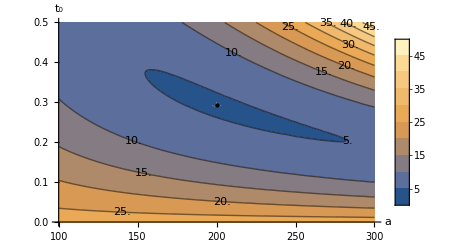

```mathematica
fig6 = Show[{ ListLinePlot[pts,Epilog->{PointSize[Medium],Point[pts]},InterpolationOrder->1],ContourPlot[J1a[k,a,T, t0]/.{k->200,T->1},{a,100,300},{t0,0,0.5},ContourLabels->All, PlotLegends->Automatic, FrameLabel->{a, ToExpression["t_0",TeXForm,HoldForm]}]},PlotRange->All,AxesOrigin->{100,0},  AxesLabel->{a,ToExpression["t_0",TeXForm,HoldForm]}]
Export["evol_figures/contour_plot_evol_case1a.pdf",fig6];
```

```mathematica
J2Plot[a_, t0_]:= Piecewise[{{Simplify[Evaluate[J1a[k,a,T, t0]/.{k->200,T->1}]],0<t0≤0.5},{Simplify[Evaluate[J2a[k,a,T, t0]/.{k->200,T->1}]],0.5<t0≤1}}];
```

```mathematica
Plot3D[J2Plot[a, t0]/.{T->1, k->200},{a,0,300}, {t0,0,1}, AxesOrigin->{0,0},AxesLabel->{a,ToExpression["t_0",TeXForm,HoldForm], J}, PlotLegends->Automatic]
```

-Graphics3D-

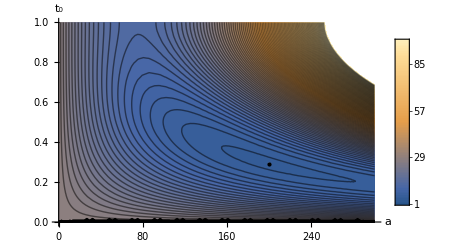

```mathematica
fig7 =  Show[{ ListLinePlot[pts,Epilog->{PointSize[Medium],Point[pts]},InterpolationOrder->1],ContourPlot[J2Plot[a, t0]/.{T->1, k->200},{a,0,300},{t0,0,1},  Contours->Range[100], PlotLegends->Automatic, PlotRange->{0,100}]},PlotRange->All,AxesOrigin->{0,0},AxesLabel->{a,ToExpression["t_0",TeXForm,HoldForm]}]
Export["evol_figures/contour_plot_evol_piecewise_linear.pdf",fig7];
```

The optimal result of the displacement field

```mathematica
optimalDis = Plot3D[u[a,b,t, x, t0]/.{ k->200, a->200, b->0, t0->0.5*(2-Sqrt[2])},{t,0,1}, {x,0,1}, AxesOrigin->{0,0},AxesLabel->{t,x, J}, PlotStyle->Directive[Gray,Specularity[White,40]]];
Export["evol_figures/optimal_displacement_field.pdf",optimalDis]
```

evol_figures/optimal_displacement_field.pdf